```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pr[list_,c_]:=Table[list⟦i⟧⟦c⟧,{i,1,Length[list]}]
```

```mathematica
resolution={1024,1024};
```

```mathematica
Import[Header<>"/PCF1.csv"];
```

# Analyse data from one file

## Import data

```mathematica
(*Export[Header<>"/number.csv",{200}]*)
```

RecData_tau0.1_num5000_vel1/number.csv

```mathematica
Header="RecData_tau0.1_num5000_vel1";
```

#### Get the number of files to expect

```mathematica
numberF=Import[Header<>"/number.csv"]⟦1⟧⟦1⟧;
```

#### Predictor data

```mathematica
predData={};
For[i=1,i≤numberF,++i,AppendTo[predData,Import[Header<>"/PCF"<>ToString[i]<>".csv"]]]
```

```mathematica
predLst=Table[{predData⟦1⟧⟦j⟧⟦1⟧,Sum[predData⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[predData]}]/Length[predData]},{j,1,Length[predData⟦1⟧]}];
```

```mathematica
predSig=Table[{predData⟦1⟧⟦j⟧⟦1⟧,(Sum[(predData⟦i⟧⟦j⟧⟦2⟧-predLst⟦j⟧⟦2⟧)^2,{i,1,Length[predData]}]/Length[predData])^(1/2)},{j,1,Length[predData⟦1⟧]}];
```

#### Gradient data

```mathematica
gradData={};
For[i=1,i≤numberF,++i,AppendTo[gradData,Import[Header<>"/GCF"<>ToString[i]<>".csv"]]]
```

```mathematica
gradLst=Table[{gradData⟦1⟧⟦j⟧⟦1⟧,Sum[gradData⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[gradData]}]/Length[gradData]},{j,1,Length[gradData⟦1⟧]}];
```

```mathematica
gradSig=Table[{gradData⟦1⟧⟦j⟧⟦1⟧,(Sum[(gradData⟦i⟧⟦j⟧⟦2⟧-gradLst⟦j⟧⟦2⟧)^2,{i,1,Length[gradData]}]/Length[gradData])^(1/2)},{j,1,Length[gradData⟦1⟧]}];
```

#### Predictor diff data

```mathematica
pDiff={};
For[i=1,i≤numberF,++i,AppendTo[pDiff,Import[Header<>"/PDiff"<>ToString[i]<>".csv"]]];
```

```mathematica
pDiffLst=Table[{pDiff⟦1⟧⟦j⟧⟦1⟧,Sum[pDiff⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[pDiff]}]/Length[pDiff]},{j,1,Length[pDiff⟦1⟧]}];
```

```mathematica
pDiffSig=Table[{pDiff⟦1⟧⟦j⟧⟦1⟧,(Sum[(pDiff⟦i⟧⟦j⟧⟦2⟧-pDiffLst⟦j⟧⟦2⟧)^2,{i,1,Length[pDiff]}]/Length[pDiff])^(1/2)},{j,1,Length[pDiff⟦1⟧]}];
```

#### Gradient diff data

```mathematica
gDiff={};
For[i=1,i≤numberF,++i,AppendTo[gDiff,Import[Header<>"/GDiff"<>ToString[i]<>".csv"]]];
```

```mathematica
gDiffLst=Table[{gDiff⟦1⟧⟦j⟧⟦1⟧,Sum[gDiff⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[gDiff]}]/Length[gDiff]},{j,1,Length[gDiff⟦1⟧]}];
```

```mathematica
gDiffSig=Table[{gDiff⟦1⟧⟦j⟧⟦1⟧,(Sum[(gDiff⟦i⟧⟦j⟧⟦2⟧-gDiffLst⟦j⟧⟦2⟧)^2,{i,1,Length[gDiff]}]/Length[gDiff])^(1/2)},{j,1,Length[gDiff⟦1⟧]}];
```

## Plots

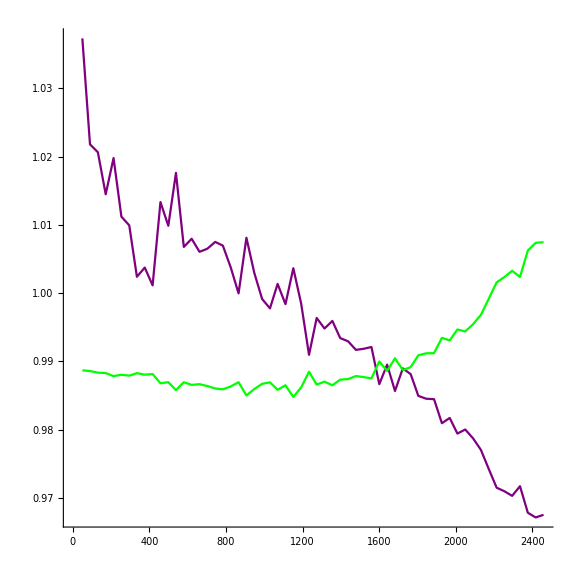

```mathematica
ListLinePlot[{predLst,gradLst},PlotStyle->{Purple,Green},ImageSize->Large,AspectRatio->1,PlotRange->All]
```

```mathematica
Quiet[Needs["ErrorBarPlots`"]]
```

#### Create predictor error plot data

```mathematica
Clear[predCF]
predCF=Partition[Riffle[pr[predLst,2],pr[predSig,2]],2];
```

#### Create gradient error plot data

```mathematica
Clear[gradCF]
gradCF=Partition[Riffle[pr[gradLst,2],pr[gradSig,2]],2];
```

#### Create graph

```mathematica
ts=Table[{i,gradLst⟦i⟧⟦1⟧},{i,1,Length[gradLst],4}];
tickSpecs={ts,Automatic};
```

```mathematica
upper=Table[Max[predLst⟦i⟧⟦2⟧+predSig⟦i⟧⟦2⟧,gradLst⟦i⟧⟦2⟧+gradSig⟦i⟧⟦2⟧],{i,1,Length[predLst]}];
lower=Table[Min[predLst⟦i⟧⟦2⟧-predSig⟦i⟧⟦2⟧,gradLst⟦i⟧⟦2⟧-gradSig⟦i⟧⟦2⟧],{i,1,Length[predLst]}];
```

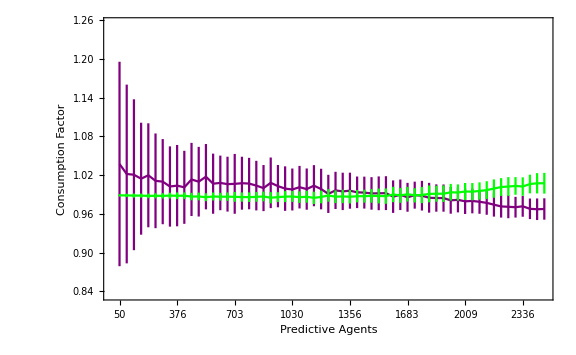

```mathematica
ErrorListPlot[{predCF,gradCF},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.95 Min[lower],1.05Max[upper]},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Purple,Green},ImageSize->Large]
```

```mathematica
plot=ErrorListPlot[{predCF,gradCF},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.95 Min[lower],1.05Max[upper]},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Purple,Green},ImageSize->resolution,AspectRatio->1];
```

```mathematica
Export[Header<>"/Cf.jpg",plot,"CompressionLevel"->0];
```

## Diff plot

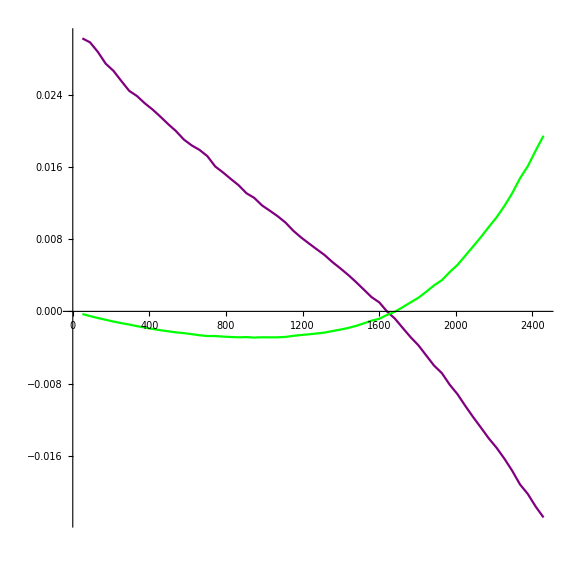

```mathematica
ListLinePlot[{pDiffLst,gDiffLst},PlotStyle->{Purple,Green},ImageSize->Large,AspectRatio->1,PlotRange->All]
```

#### Create predictor error plot data

```mathematica
Clear[pDiffErr]
pDiffErr=Partition[Riffle[pr[pDiffLst,2],pr[pDiffSig,2]],2];
```

#### Create gradient error plot data

```mathematica
Clear[gDiffErr]
gDiffErr=Partition[Riffle[pr[gDiffLst,2],pr[gDiffSig,2]],2];
```

#### Create graph

```mathematica
ts=Table[{i,gradLst⟦i⟧⟦1⟧},{i,1,Length[gradLst],4}];
tickSpecs={ts,Automatic};
```

```mathematica
upper=Table[Max[pDiffLst⟦i⟧⟦2⟧+pDiffSig⟦i⟧⟦2⟧,gDiffLst⟦i⟧⟦2⟧+gDiffSig⟦i⟧⟦2⟧],{i,1,Length[pDiffLst]}];
lower=Table[Min[pDiffLst⟦i⟧⟦2⟧-pDiffSig⟦i⟧⟦2⟧,gDiffLst⟦i⟧⟦2⟧-gDiffSig⟦i⟧⟦2⟧],{i,1,Length[pDiffLst]}];
```

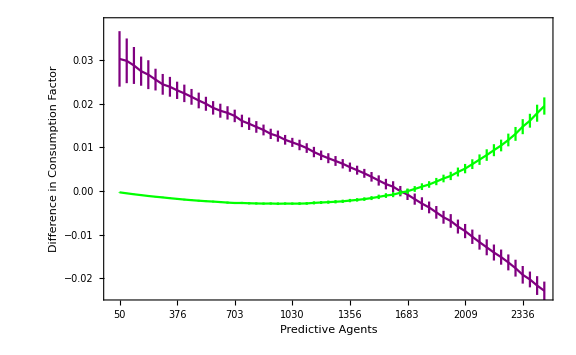

```mathematica
ErrorListPlot[{pDiffErr,gDiffErr},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.95 Min[lower],1.05Max[upper]},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Purple,Green},ImageSize->Large]
```

```mathematica
plot=ErrorListPlot[{pDiffErr,gDiffErr},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.95 Min[lower],1.05Max[upper]},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Purple,Green},ImageSize->resolution,AspectRatio->1];
```

```mathematica
Export[Header<>"/Diff.jpg",plot,"CompressionLevel"->0];
```

# Analyse Data from different files

## Functions for getting data from a file

### Predictive difference getters

```mathematica
GetPDiffLst[fileName_]:=({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,

pDiff={},

For[i=1,i≤num,++i,AppendTo[pDiff,Import[fileName<>"/PDiff"<>ToString[i]<>".csv"]]],

Table[{pDiff⟦1⟧⟦j⟧⟦1⟧,Sum[pDiff⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[pDiff]}]/Length[pDiff]},{j,1,Length[pDiff⟦1⟧]}]
})⟦4⟧
```

```mathematica
GetPDiffErr[fileName_]:=({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,

pDiff={},

For[i=1,i≤num,++i,AppendTo[pDiff,Import[fileName<>"/PDiff"<>ToString[i]<>".csv"]]],

Table[{pDiff⟦1⟧⟦j⟧⟦1⟧,(Sum[(pDiff⟦i⟧⟦j⟧⟦2⟧-pDiffLst⟦j⟧⟦2⟧)^2,{i,1,Length[pDiff]}]/Length[pDiff])^(1/2)},{j,1,Length[pDiff⟦1⟧]}]
})⟦4⟧
```

```mathematica
CreatePDiffEP[fileName_]:=({
p1=GetPDiffLst[fileName];,
p2=GetPDiffErr[fileName];,
Partition[Riffle[pr[p1,2],pr[p2,2]],2]
})⟦3⟧
```

### Gradient difference getters

```mathematica
GetGDiffLst[fileName_]:=({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,

gDiff={},

For[i=1,i≤num,++i,AppendTo[gDiff,Import[fileName<>"/GDiff"<>ToString[i]<>".csv"]]],

Table[{gDiff⟦1⟧⟦j⟧⟦1⟧,Sum[gDiff⟦i⟧⟦j⟧⟦2⟧,{i,1,Length[gDiff]}]/Length[gDiff]},{j,1,Length[gDiff⟦1⟧]}]
})⟦4⟧
```

```mathematica
GetGDiffErr[fileName_]:=({
num=Import[fileName<>"/number.csv"]⟦1⟧⟦1⟧,

gDiff={},

For[i=1,i≤num,++i,AppendTo[gDiff,Import[fileName<>"/GDiff"<>ToString[i]<>".csv"]]],

Table[{gDiff⟦1⟧⟦j⟧⟦1⟧,(Sum[(gDiff⟦i⟧⟦j⟧⟦2⟧-gDiffLst⟦j⟧⟦2⟧)^2,{i,1,Length[gDiff]}]/Length[gDiff])^(1/2)},{j,1,Length[gDiff⟦1⟧]}]
})⟦4⟧
```

```mathematica
CreateGDiffEP[fileName_]:=({
g1=GetGDiffLst[fileName];,
g2=GetGDiffErr[fileName];,
Partition[Riffle[pr[g1,2],pr[g2,2]],2]
})⟦3⟧
```

## Plot

#### With error data

```mathematica
pdt03e=CreatePDiffEP["RecData_tau0.03_num5000_vel1"];
gdt03e=CreateGDiffEP["RecData_tau0.03_num5000_vel1"];
pdt05e=CreatePDiffEP["RecData_tau0.05_num5000_vel1"];
gdt05e=CreateGDiffEP["RecData_tau0.05_num5000_vel1"];
pdt08e=CreatePDiffEP["RecData_tau0.08_num5000_vel1"];
gdt08e=CreateGDiffEP["RecData_tau0.08_num5000_vel1"];
pdt10e=CreatePDiffEP["RecData_tau0.1_num5000_vel1"];
gdt10e=CreateGDiffEP["RecData_tau0.1_num5000_vel1"];
```

#### Without error data

```mathematica
pdt03=GetPDiffLst["RecData_tau0.03_num5000_vel1"];
gdt03=GetGDiffLst["RecData_tau0.03_num5000_vel1"];
pdt05=GetPDiffLst["RecData_tau0.05_num5000_vel1"];
gdt05=GetGDiffLst["RecData_tau0.05_num5000_vel1"];
pdt08=GetPDiffLst["RecData_tau0.08_num5000_vel1"];
gdt08=GetGDiffLst["RecData_tau0.08_num5000_vel1"];
pdt10=GetPDiffLst["RecData_tau0.1_num5000_vel1"];
gdt10=GetGDiffLst["RecData_tau0.1_num5000_vel1"];
```

#### Plot

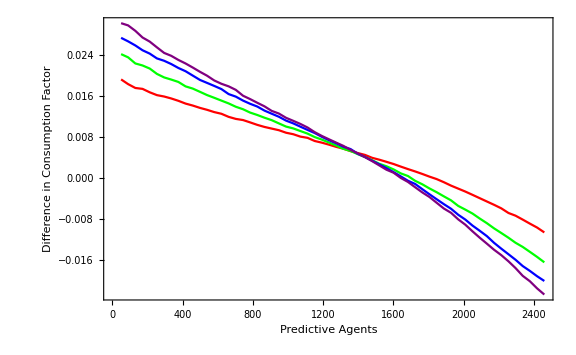

```mathematica
ListLinePlot[{pdt03,pdt05,pdt08,pdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Red,Green,Blue,Purple},ImageSize->Large]
```

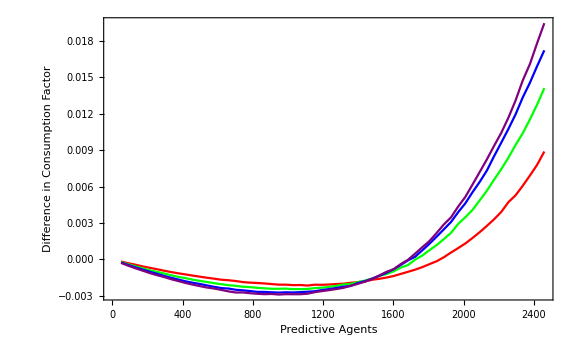

```mathematica
ListLinePlot[{gdt03,gdt05,gdt08,gdt10},Frame->True,FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Red,Green,Blue,Purple},ImageSize->Large]
```

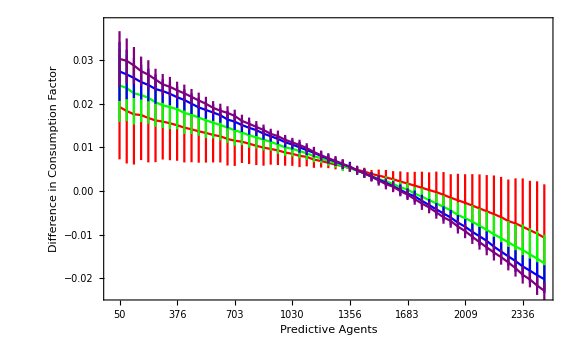

```mathematica
ErrorListPlot[{pdt03e,pdt05e,pdt08e,pdt10e},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.95 Min[lower],1.05Max[upper]},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Red,Green,Blue,Purple},ImageSize->Large]
```

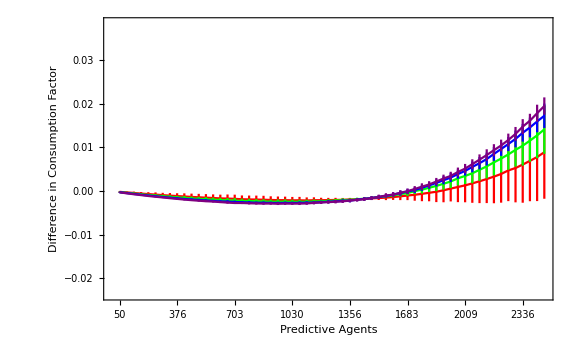

```mathematica
ErrorListPlot[{gdt03e,gdt05e,gdt08e,gdt10e},Joined->True,Frame->True,FrameTicks->tickSpecs,PlotRange->{0.95 Min[lower],1.05Max[upper]},FrameLabel->{Style["Predictive Agents",12,FontFamily->"Arial"],Style["Difference in Consumption Factor",12,FontFamily->"Arial"]},PlotStyle->{Red,Green,Blue,Purple},ImageSize->Large]
```